## Q2)

Initializations

## Defining functions and constants

```mathematica
SeedRandom[];

n=100000; (*Number of particles*)

G=1;R=1;M=1;

ne=5;  (*The parameter n in the question*)

ϕ[r_]=-G M (3 R^2-r^2)/(2 R^3); (*Potential energy inside a uniform sphere *) 

vm[r_]=Sqrt[-2ϕ[r]]; (*Maximum allowed velocity for a particle at r*)

f[e_]=If[e>0,F e^(ne-3/2),0]//Simplify;(*Distribution function*)

e[v_,r_]=-v^2/2-ϕ[r];
```

## Defining distribution function in terms of v and r

### Numerically integrating to find normalization constant F:

```mathematica
sF={F->1/NIntegrate[(4Pi)^2r^2 v^2 f[e[v,r]]/.{F->1},{r,0,R},{v,0,vm[r]}]}
```

{F→0.0558656}

### Analytically finding normalization constant F:

```mathematica
sF=Solve[Integrate[(4Pi)^2r^2 v^2 f[e[v,r]],{r,0,R},{v,0,vm[r]}]==1,F]
```

{{F→(572 √2)/(467 π^3)}}

```mathematica
sF[[1]]//N
```

{F→0.0558656}

### Substituting the value of F in the distribution function:

```mathematica
f[v_,r_]=f[e[v,r]]/.sF[[1]]//N//Simplify
```

Piecewise[{{0.0558656 (1.5-0.5 r^2-0.5 v^2)^(7/2), 1. r^2+1. v^2<3.}, {0., True}}]

This is the normalized distribution function as a function of the magnitudes of velocities and radial distances.

## Distributing initial positions randomly inside a sphere

```mathematica
x0=RandomPoint[Ball[{2,2,2},1],n]; (*Initial positions of particles*)
```

### The radial distance of each point is given by:

```mathematica
xi=Norm[#-{2,2,2}]&/@x0;
```

### Plot of initial distribution of positions:

```mathematica
ListPointPlot3D[x0[[1;;n/10]],BoxRatios->{1,1,1},ImageSize->Medium,ColorFunction->Function[{x,y,z},RGBColor@@RandomReal[1,3]]]
```

-Graphics3D-

## Calculating the probability distribution function for velocity at a particular r

### Renormalizing the distribution function at each value of r:

```mathematica
p[v_,r_]=v^2f[v,r]/Integrate[v^2f[v,r],{v,0,vm[r]},Assumptions->r^2<1];
```

### Function to calculate the overall velocity distribution:

```mathematica
fv[v_]:= NIntegrate[3r^2 p[v,r],{r,0,1}];
```

## Method 1: Inverse transform sampling with numerical rootfinding

### Finding the CDF analytically:

```mathematica
cpv[x_,r_]=Integrate[p[v,r],{v,0,x},Assumptions->{0<x<vm[r],0<=r<=1}]//Simplify;
```

### Finding the inverse of the CDF using the secant method:

```mathematica
rv[r_]:=FindRoot[cpv[x,r]==RandomReal[],{x,0.001,vm[r]-.001}][[1]][[2]]
```

### Randomly picking velocities at each point using the above method:

```mathematica
vi=rv/@xi;
```

### Comparing obtained distribution of velocities with the expected distribution:

```mathematica
vplot=Plot[fv[v],{v,0,vm[0]},PlotStyle->Red];
```

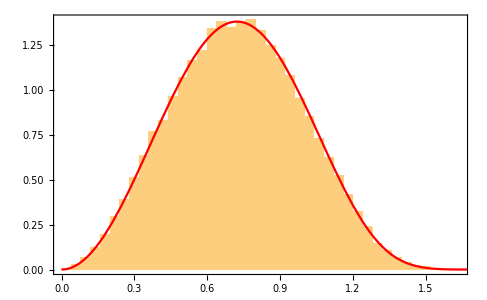

```mathematica
Show[Histogram[vi,{.04},PDF,Frame->True],vplot]
```

## Method 2: Using built-in functions for probabilty distributions:

```mathematica
pv[r_]=ProbabilityDistribution[p[v,r],{v,0,vm[r]}];
```

### Plots of the PDF of velocities for different values of r:

r = 0.0, 0.1, 0.2, 0.3, ..., 0.9, 1.0

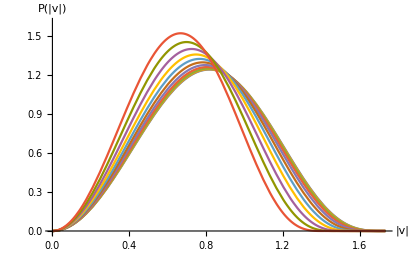

```mathematica
Plot[Evaluate[Table[PDF[pv[r],x],{r,0,1,.1}]],{x,0,vm[0]},PlotRange->{0,1.6},AxesLabel->{HoldForm["|v|"],HoldForm["P(|v|)"]}]
```

### The magnitude of initial velocities is given by:

```mathematica
vi=RandomVariate[pv[#]]&/@xi;
```

$Aborted

```mathematica
vi=Norm[#]&/@v0;
```

```mathematica
vi={};
```

### Appending more values of |x| and |v|

```mathematica
While[Length[vi]<n,AppendTo[vi,RandomVariate[pv[xi[[Length[vi]+1]]]]]];
```

```mathematica
Dynamic[Length[vi]]
```

### Comparing obtained distribution of velocities with the expected distribution:

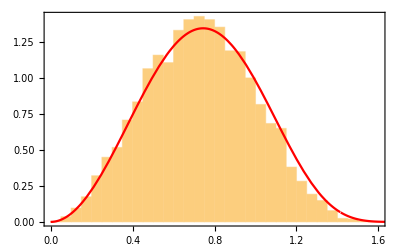

```mathematica
Histogram[vt,Automatic,PDF,Epilog->First@Plot[fv[x],{x,0,vm[0]},PlotStyle->Red],Frame->True]
```

### Generating random unit vectors for directions for velocities

```mathematica
n0=RandomPoint[Sphere[],n];(*Gives random points on the surface of a unit sphere*)
```

### Multiplying the unit vectors with the magnitudes to get the initial velocities:

```mathematica
v0=vi*n0;(*Initial velocities of particles*)
```

### Plot of initial distribution of velocities:

```mathematica
ListPointPlot3D[v0[[1;;n/2]],BoxRatios->{1,1,1},ImageSize->Medium,ColorFunction->Function[{x,y,z},RGBColor@RandomReal[1,3]]]
```

-Graphics3D-

## Calculating virial ratio:

### Kinetic energy:

```mathematica
K=1/2Total[vi^2]
```

2992.31

### Potential energy:

```mathematica
W=Total[ϕ/@xi]
```

-12000.

### The virial ratio is:

```mathematica
2K/Abs[W]
```

0.498718

## Writing data to files

```mathematica
Export["A://x0-50000",x0,"Table"];
Export["A://v0-50000",v0,"Table"];
```

## Extracting data from files

```mathematica
x0=Import["A:\\x0-50000","Table"];
v0=Import["A:\\v0-50000","Table"];
xi=Norm[#-{2,2,2}]&/@x0;vi=Norm[#]&/@v0;
```